```mathematica
ElementaryCellularAutomaton[r_,n_]:=CellularAutomaton[r,{{1},0},n];
```

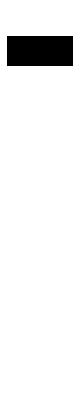

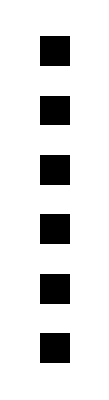

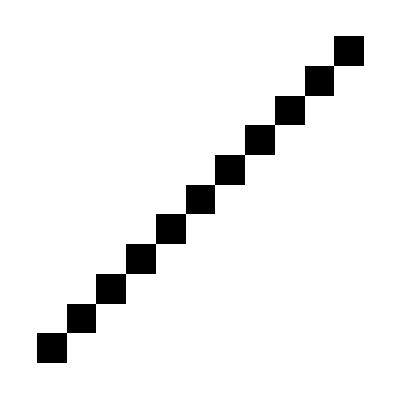

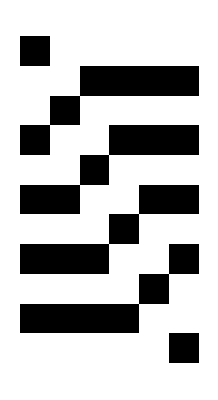

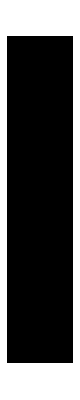

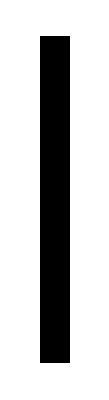

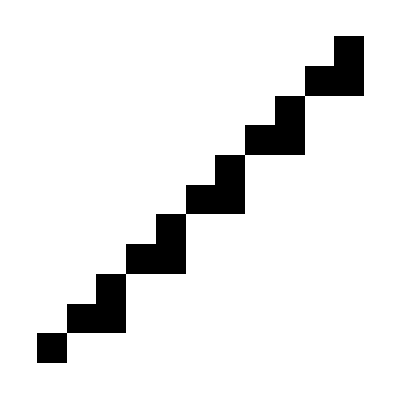

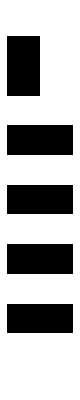

-Graphics-

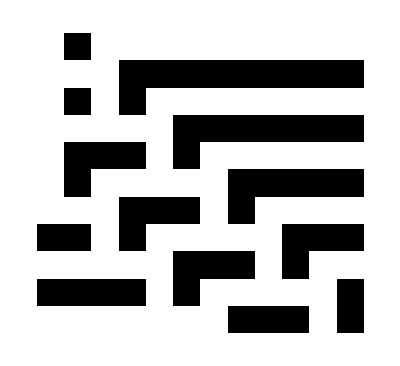

-Graphics-

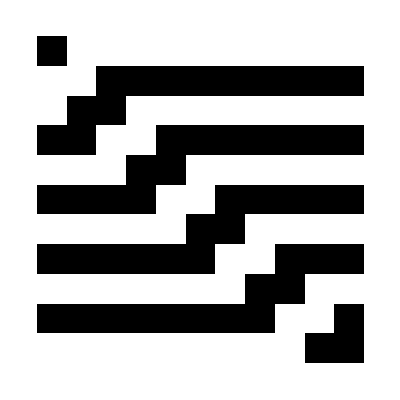

-Graphics-

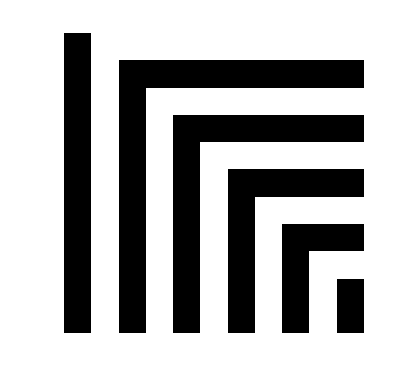

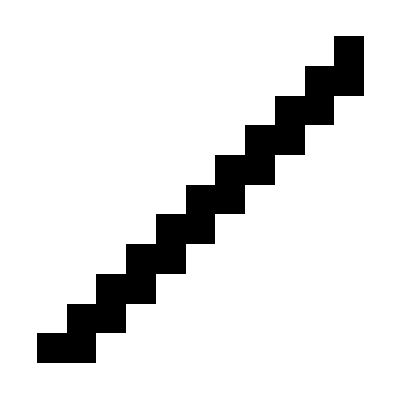

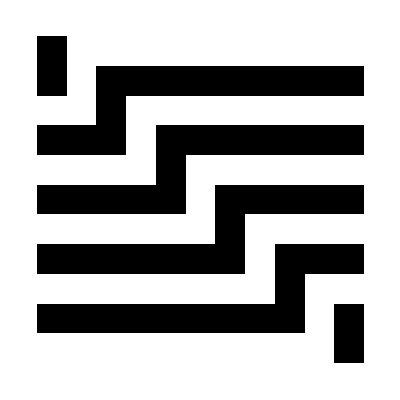

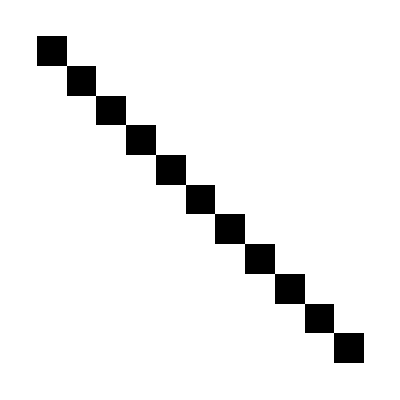

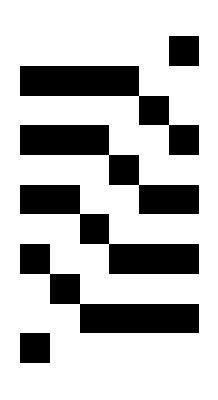

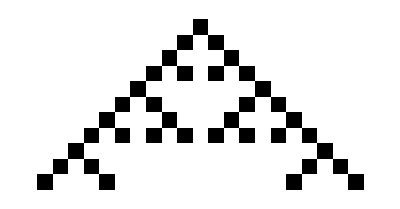

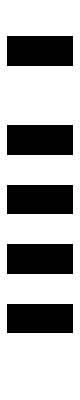

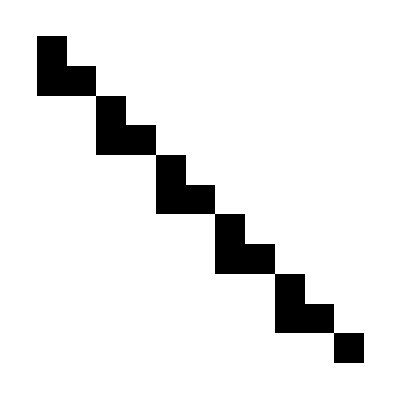

-Graphics-

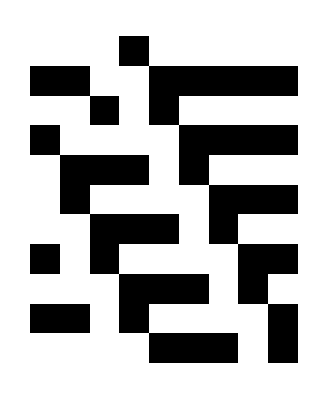

-Graphics-

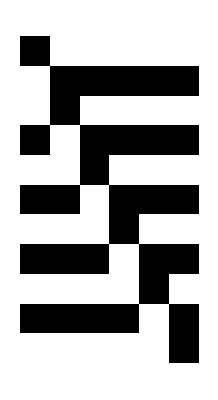

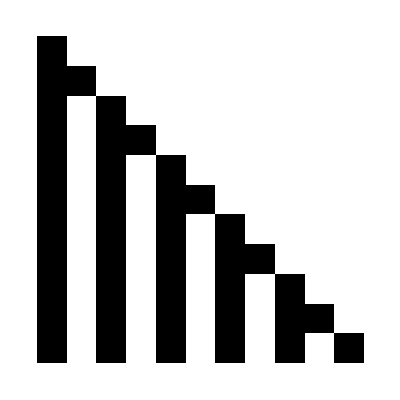

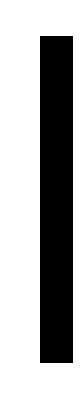

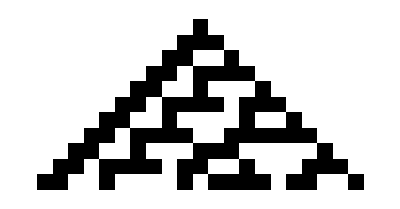

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

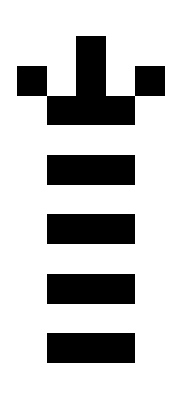

-Graphics-

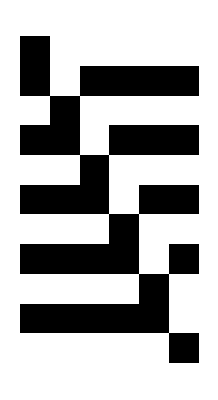

-Graphics-

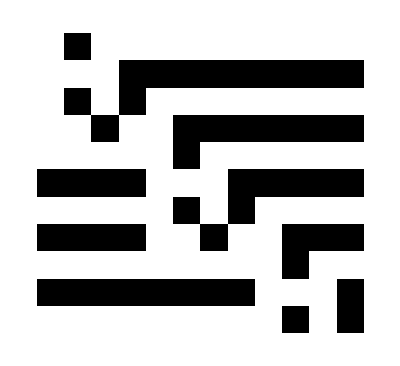

-Graphics-

-Graphics-

-Graphics-

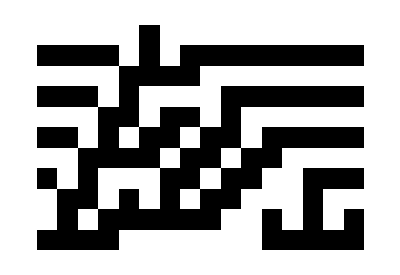

-Graphics-

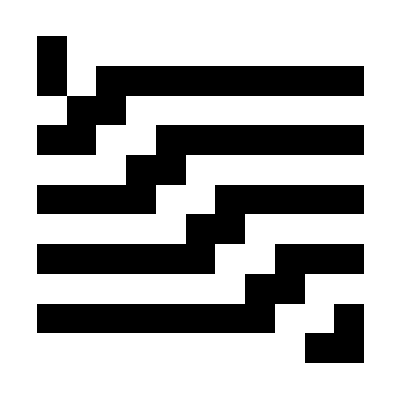

-Graphics-

-Graphics-

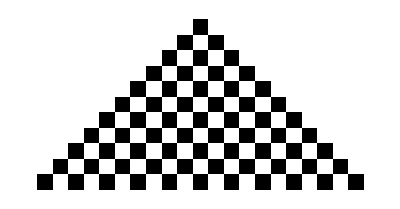

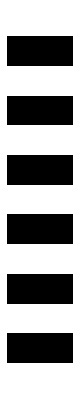

-Graphics-

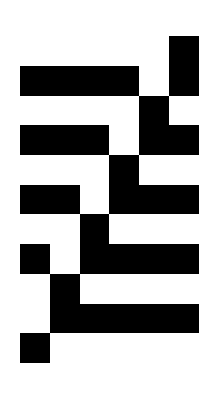

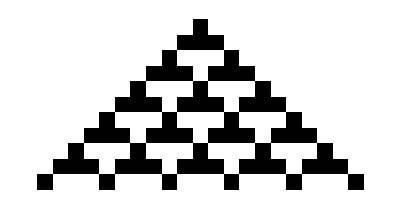

-Graphics-

-Graphics-

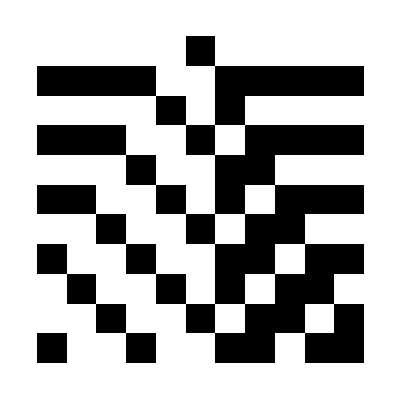

-Graphics-

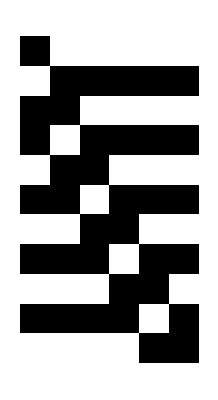

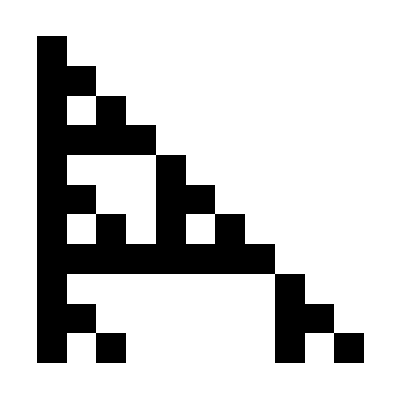

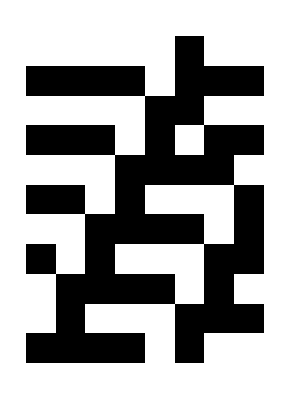

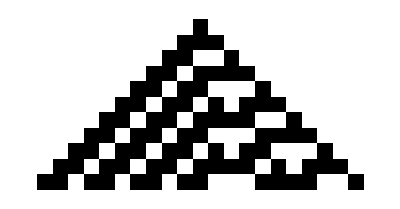

-Graphics-

-Graphics-

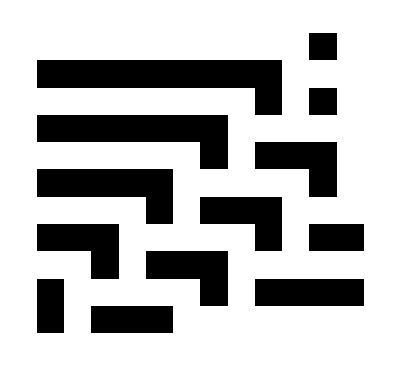

-Graphics-

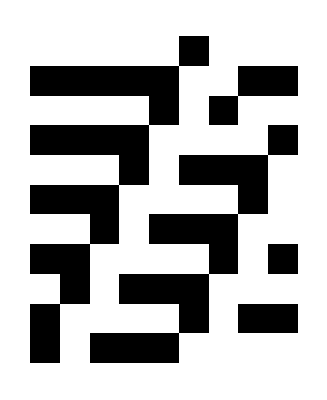

-Graphics-

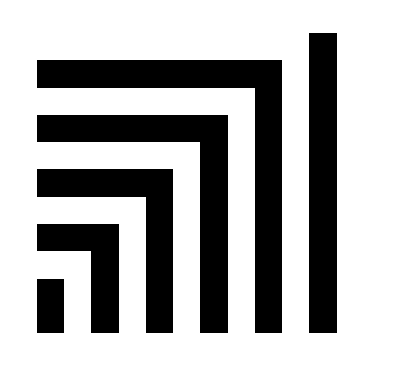

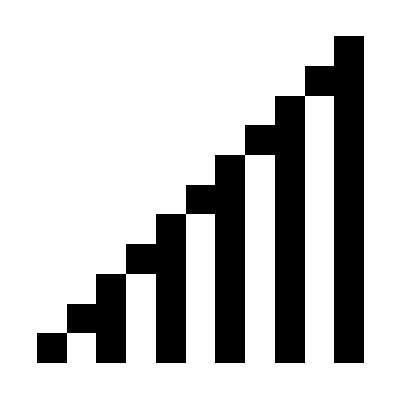

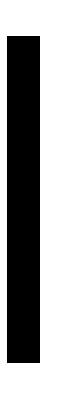

-Graphics-

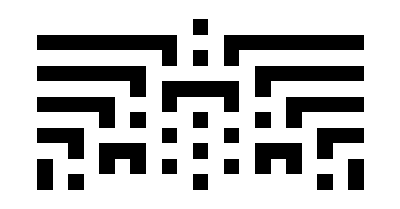

-Graphics-

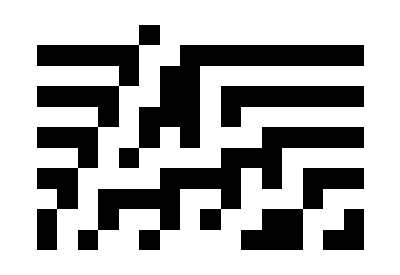

-Graphics-

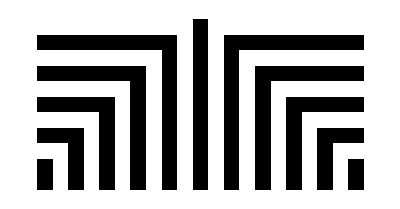

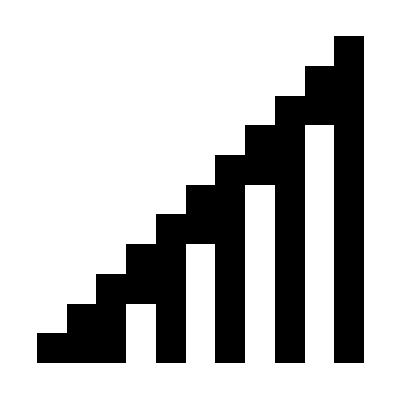

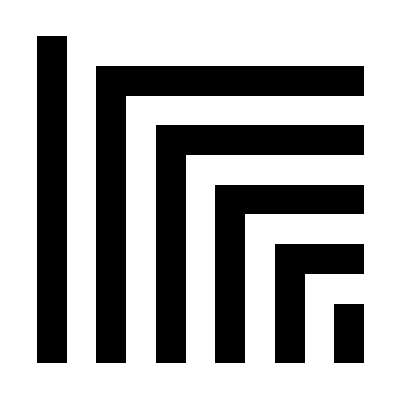

-Graphics-

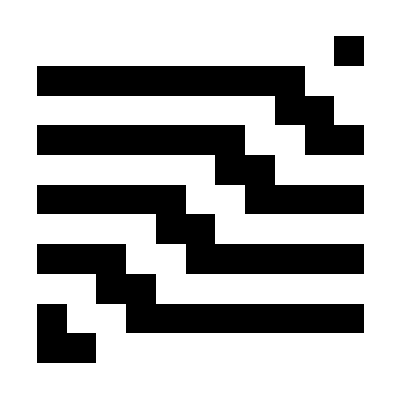

-Graphics-

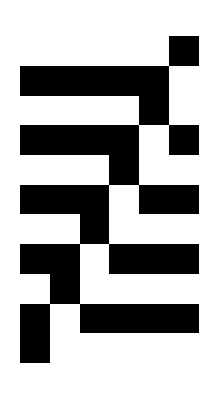

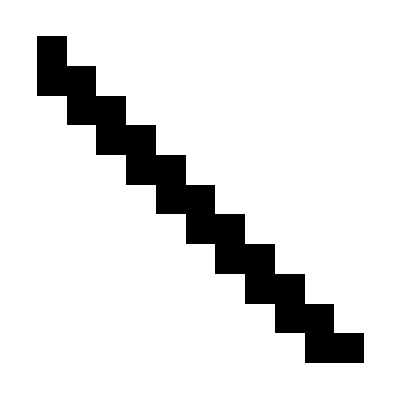

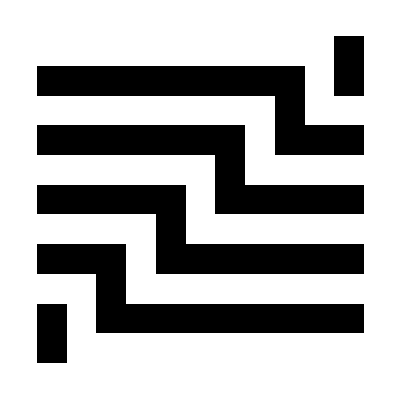

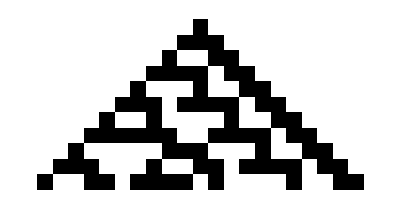

-Graphics-

-Graphics-

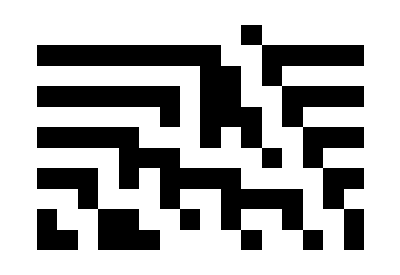

-Graphics-

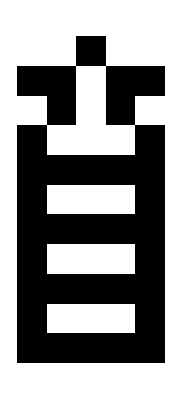

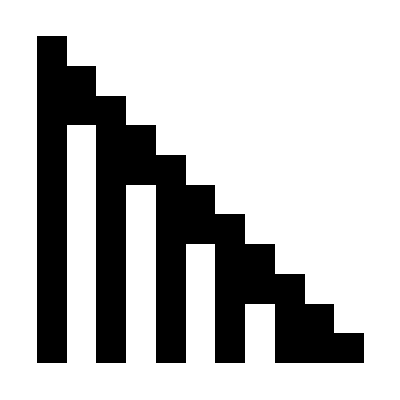

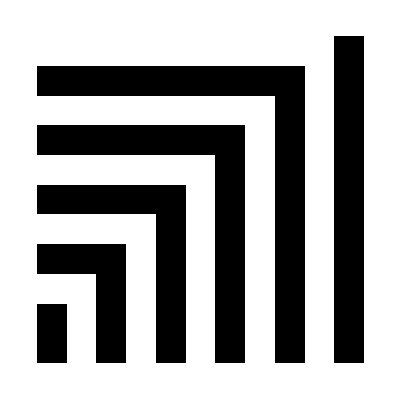

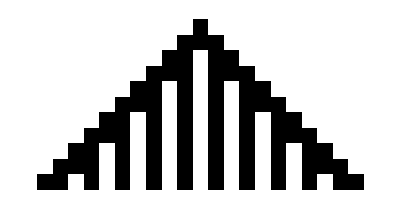

-Graphics-

-Graphics-

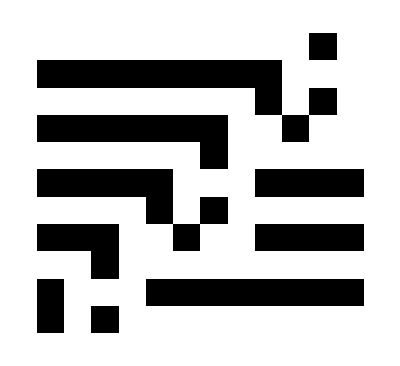

-Graphics-

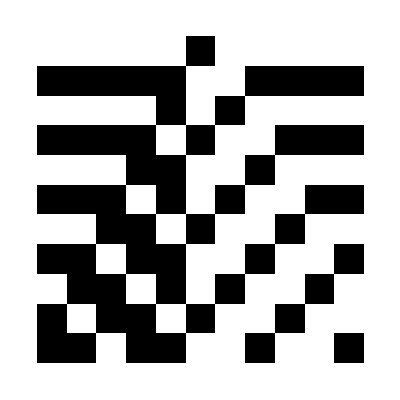

-Graphics-

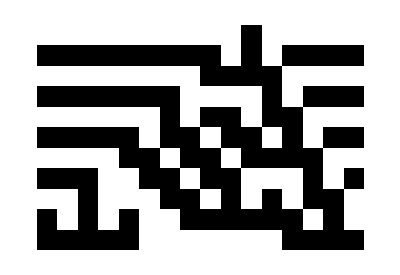

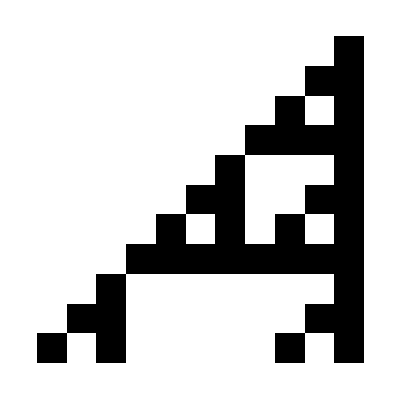

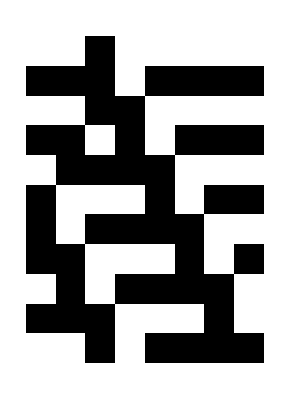

-Graphics-

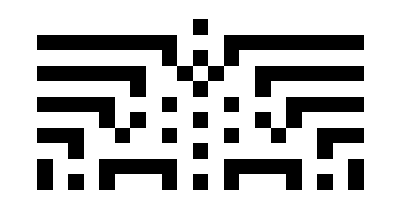

-Graphics-

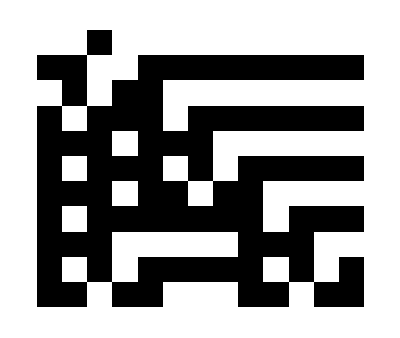

-Graphics-

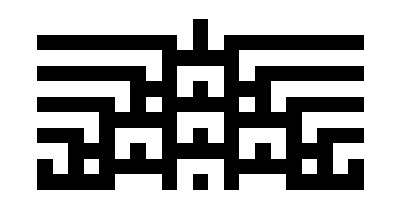

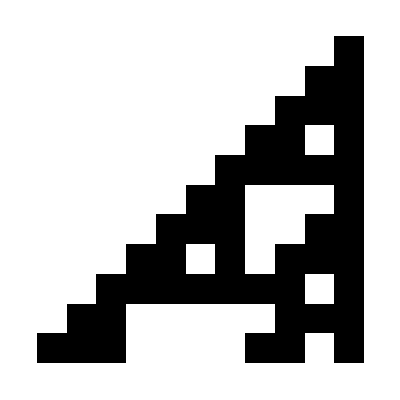

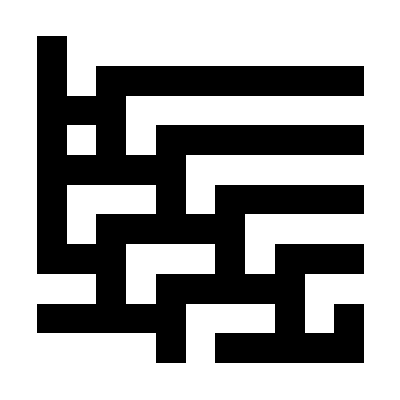

-Graphics-

-Graphics-

-Graphics-

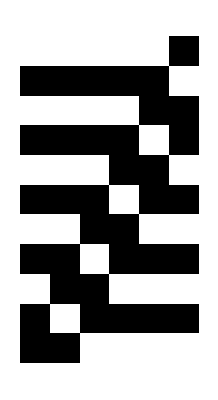

-Graphics-

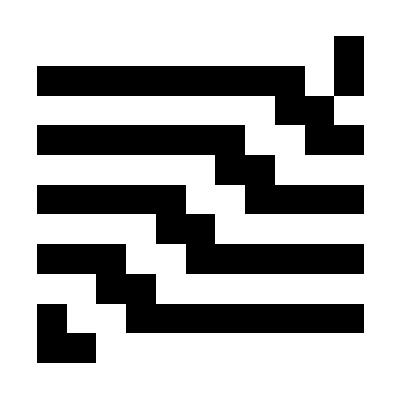

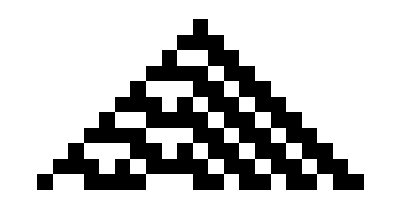

-Graphics-

-Graphics-

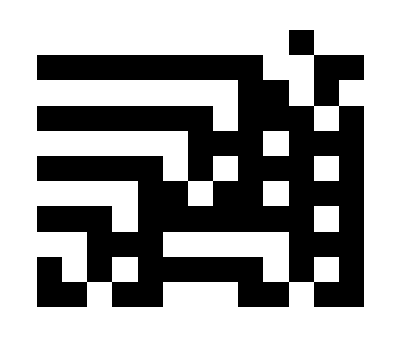

-Graphics-

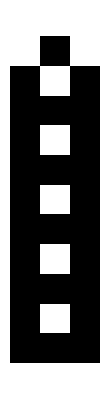

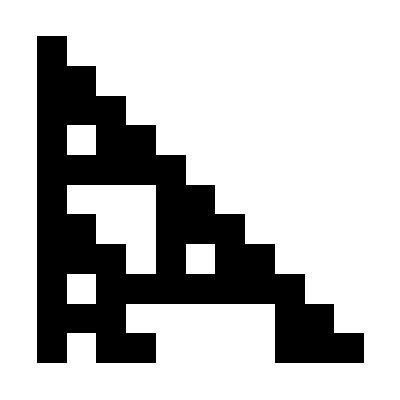

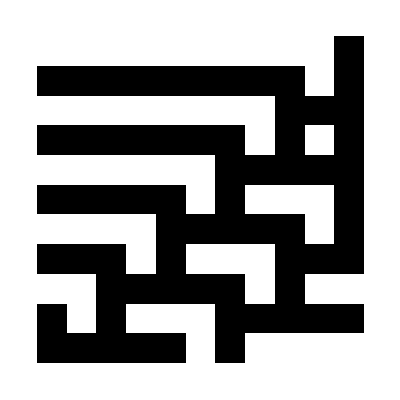

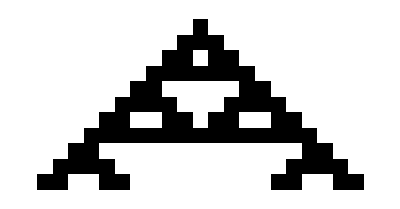

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«125 more identical outputs»

```mathematica
For[i = 0, i ≤ 255, i++, esp = ElementaryCellularAutomaton[i, 10];
Print[ArrayPlot[esp]]]
```

```mathematica
ArrayPlot[ElementaryCellularAutomaton[30, 300]]
```

-Graphics-

```mathematica
FromDigits[#,2]&/@With[{n=10},MapIndexed[Take[#1,n+#2[[1]]{-1,1}+{2,0}]&,ElementaryCellularAutomaton[30,n]]]
```

{1,7,25,111,401,1783,6409,28479,102849,456263,1641433}

```mathematica
rules=Flatten[Transpose[Partition[l={30,54,60,62,90,94,102,110,122,126,150,158,182,188,190,220,222,250},Ceiling[Length[l]/2],Ceiling[Length[l]/2],{1,1},{{}}]]]
```

{30,126,54,150,60,158,62,182,90,188,94,190,102,220,110,222,122,250}

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

```mathematica
Show[ArrayPlot[ElementaryCellularAutomaton[90, 200]]]
```

-Graphics-